```mathematica
β[ω_,δ_,t_,ϵ_]:=β[ω,δ,t,ϵ]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[8],Join[Table[{i,i-1},{i,Range[2,8,1]}],Table[{i,i+1},{i,Range[1,8,1]}]]->-t]
```

```mathematica
T[t_]:=T[t]=t*IdentityMatrix[8]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,δ,1,0]],A:=Inverse[β[ω,δ,1,0]],T:=T[1]},Do[J=Inverse[IdentityMatrix[8]-A.T.J.T].A,60000];J=J]
```

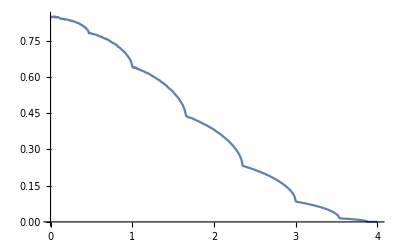

```mathematica
ListLinePlot[Table[{ω,-Im[LEFT[ω,0.0001,1,0]][[1,1]]},{ω,Range[0,4,0.01]}]]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[8]-g[ω,δ,t,ϵ].T[1].LEFT[ω,δ,t,ϵ].T[1]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[8]-g[ω,δ,t,ϵ].T[1].LEFT[ω,δ,t,ϵ].T[1]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[8]-SL[ω,δ,1,0].T[1].SR[ω,δ,1,0].T[1]].SL[ω,δ,1,0]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[8]-SR[ω,δ,1,0].T[1].SL[ω,δ,1,0].T[1]].SR[ω,δ,1,0]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,1,0].T[1].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Tr[gdd[ω,δ,t,ϵ].T[1].grr[ω,δ,t,ϵ].T[1]-T[1].GNON[ω,δ,t,ϵ].T[1].GNON[ω,δ,t,ϵ]]
```

```mathematica
pris=Table[{ω,Abs[tr[ω,0.0001,1,0]]},{ω,Range[0,4,0.01]}]
```

{{0.,7.99996},{0.01,7.99996},{0.02,7.99998},{0.03,7.99998},{0.04,7.99998},{0.05,7.99997},{0.06,7.99996},{0.07,7.99997},{0.08,7.99999},{0.09,7.99996},{0.1,7.99996},{0.11,7.99994},{0.12,7.9935},{0.13,7.},{0.14,6.99999},{0.15,6.99999},{0.16,6.99998},{0.17,6.99998},{0.18,6.99997},{0.19,6.99998},{0.2,6.99997},{0.21,6.99998},{0.22,6.99996},{0.23,6.99999},{0.24,6.99998},{0.25,6.99997},{0.26,6.99997},{0.27,6.99998},{0.28,6.99999},{0.29,6.99998},{0.3,6.99999},{0.31,6.99998},{0.32,6.99998},{0.33,6.99997},{0.34,6.99998},{0.35,6.99998},{0.36,6.99999},{0.37,6.99997},{0.38,6.99997},{0.39,6.99998},{0.4,6.99997},{0.41,6.99996},{0.42,6.99996},{0.43,6.99997},{0.44,6.99997},{0.45,6.99997},{0.46,6.99994},{0.47,6.00053},{0.48,5.99999},{0.49,5.99998},{0.5,5.99998},{0.51,5.99995},{0.52,5.99998},{0.53,5.99999},{0.54,5.99997},{0.55,5.99996},{0.56,5.99996},{0.57,5.99999},{0.58,5.99997},{0.59,5.99997},{0.6,5.99999},{0.61,5.99996},{0.62,5.99997},{0.63,5.99998},{0.64,5.99999},{0.65,5.99998},{0.66,5.99997},{0.67,5.99999},{0.68,5.99996},{0.69,5.99996},{0.7,5.99998},{0.71,5.99997},{0.72,5.99999},{0.73,5.99998},{0.74,5.99997},{0.75,5.99998},{0.76,5.99997},{0.77,5.99998},{0.78,5.99999},{0.79,5.99997},{0.8,5.99996},{0.81,5.99997},{0.82,5.99999},{0.83,5.99997},{0.84,5.99997},{0.85,5.99999},{0.86,5.99996},{0.87,5.99999},{0.88,5.99999},{0.89,5.99996},{0.9,5.99998},{0.91,5.99998},{0.92,5.99998},{0.93,5.99997},{0.94,5.99996},{0.95,5.99995},{0.96,5.99997},{0.97,5.99995},{0.98,5.99996},{0.99,5.99993},{1.,5.49995},{1.01,4.99998},{1.02,4.99996},{1.03,4.99996},{1.04,4.99995},{1.05,4.99995},{1.06,4.99997},{1.07,4.99996},{1.08,4.99997},{1.09,4.99998},{1.1,4.99997},{1.11,4.99996},{1.12,4.99998},{1.13,4.99998},{1.14,4.99997},{1.15,4.99998},{1.16,4.99997},{1.17,4.99995},{1.18,4.99997},{1.19,4.99997},{1.2,4.99997},{1.21,4.99999},{1.22,4.99997},{1.23,4.99997},{1.24,4.99995},{1.25,4.99998},{1.26,4.99995},{1.27,4.99996},{1.28,5.},{1.29,4.99998},{1.3,4.99998},{1.31,4.99999},{1.32,4.99998},{1.33,4.99998},{1.34,4.99998},{1.35,4.99998},{1.36,4.99996},{1.37,4.99997},{1.38,4.99996},{1.39,4.99995},{1.4,4.99997},{1.41,4.99998},{1.42,4.99994},{1.43,4.99997},{1.44,4.99996},{1.45,4.99997},{1.46,4.99995},{1.47,4.99997},{1.48,4.99996},{1.49,4.99995},{1.5,4.99995},{1.51,4.99996},{1.52,4.99996},{1.53,4.99996},{1.54,4.99997},{1.55,4.99995},{1.56,4.99997},{1.57,4.99995},{1.58,4.99996},{1.59,4.99997},{1.6,4.99998},{1.61,4.99998},{1.62,4.99996},{1.63,4.99997},{1.64,4.99994},{1.65,4.99963},{1.66,4.00004},{1.67,3.99998},{1.68,3.99999},{1.69,3.99997},{1.7,3.99997},{1.71,3.99997},{1.72,3.99999},{1.73,3.99996},{1.74,3.99997},{1.75,3.99997},{1.76,3.99999},{1.77,3.99998},{1.78,3.99996},{1.79,3.99998},{1.8,3.99999},{1.81,3.99998},{1.82,3.99997},{1.83,3.99997},{1.84,3.99998},{1.85,3.99997},{1.86,3.99997},{1.87,3.99996},{1.88,3.99997},{1.89,3.99997},{1.9,3.99997},{1.91,3.99998},{1.92,3.99996},{1.93,3.99996},{1.94,3.99996},{1.95,3.99996},{1.96,3.99998},{1.97,3.99998},{1.98,3.99998},{1.99,3.99997},{2.,3.99997},{2.01,3.99998},{2.02,3.99997},{2.03,3.99998},{2.04,3.99996},{2.05,3.99998},{2.06,3.99999},{2.07,3.99997},{2.08,3.99997},{2.09,3.99996},{2.1,3.99997},{2.11,4.},{2.12,3.99997},{2.13,3.99997},{2.14,3.99998},{2.15,3.99999},{2.16,3.99998},{2.17,3.99999},{2.18,3.99999},{2.19,3.99998},{2.2,3.99998},{2.21,3.99999},{2.22,4.},{2.23,3.99999},{2.24,3.99999},{2.25,3.99999},{2.26,3.99998},{2.27,3.99998},{2.28,4.},{2.29,3.99999},{2.3,3.99998},{2.31,3.99999},{2.32,3.99997},{2.33,3.99997},{2.34,3.99994},{2.35,3.00034},{2.36,3.},{2.37,2.99998},{2.38,2.99999},{2.39,2.99999},{2.4,2.99999},{2.41,2.99999},{2.42,3.},{2.43,2.99998},{2.44,2.99999},{2.45,2.99998},{2.46,3.},{2.47,2.99998},{2.48,2.99999},{2.49,2.99999},{2.5,2.99999},{2.51,3.},{2.52,2.99999},{2.53,3.},{2.54,2.99999},{2.55,2.99999},{2.56,2.99999},{2.57,3.},{2.58,2.99999},{2.59,3.},{2.6,2.99999},{2.61,2.99999},{2.62,3.},{2.63,2.99999},{2.64,3.},{2.65,2.99999},{2.66,3.},{2.67,2.99999},{2.68,2.99999},{2.69,2.99999},{2.7,2.99999},{2.71,2.99999},{2.72,2.99999},{2.73,3.},{2.74,2.99999},{2.75,2.99999},{2.76,3.},{2.77,3.},{2.78,2.99999},{2.79,3.},{2.8,2.99999},{2.81,3.},{2.82,3.},{2.83,3.},{2.84,3.},{2.85,3.},{2.86,3.},{2.87,3.},{2.88,3.},{2.89,3.},{2.9,3.},{2.91,3.},{2.92,3.},{2.93,3.},{2.94,3.},{2.95,3.},{2.96,3.},{2.97,3.},{2.98,2.99999},{2.99,2.99997},{3.,2.49999},{3.01,2.00002},{3.02,2.},{3.03,2.},{3.04,2.},{3.05,2.},{3.06,2.},{3.07,2.},{3.08,2.},{3.09,2.},{3.1,2.},{3.11,2.},{3.12,2.},{3.13,2.},{3.14,2.},{3.15,2.},{3.16,2.},{3.17,2.},{3.18,2.},{3.19,2.},{3.2,2.},{3.21,2.},{3.22,2.},{3.23,2.},{3.24,2.},{3.25,2.},{3.26,2.},{3.27,2.},{3.28,2.},{3.29,2.},{3.3,2.},{3.31,2.},{3.32,2.},{3.33,2.},{3.34,2.},{3.35,2.},{3.36,2.},{3.37,2.},{3.38,2.},{3.39,2.},{3.4,2.},{3.41,2.},{3.42,2.},{3.43,2.},{3.44,2.},{3.45,2.},{3.46,2.},{3.47,2.},{3.48,2.},{3.49,2.},{3.5,2.},{3.51,1.99999},{3.52,1.99998},{3.53,1.99943},{3.54,1.00004},{3.55,1.00001},{3.56,1.},{3.57,1.},{3.58,1.},{3.59,1.},{3.6,1.},{3.61,1.},{3.62,1.},{3.63,1.},{3.64,1.},{3.65,1.},{3.66,1.},{3.67,1.},{3.68,1.},{3.69,1.},{3.7,1.},{3.71,1.},{3.72,1.},{3.73,1.},{3.74,1.},{3.75,1.},{3.76,1.},{3.77,1.},{3.78,1.},{3.79,1.},{3.8,1.},{3.81,0.999999},{3.82,0.999999},{3.83,0.999999},{3.84,0.999998},{3.85,0.999997},{3.86,0.999993},{3.87,0.999972},{3.88,0.00648459},{3.89,0.0000220888},{3.9,5.84101×10^-6},{3.91,2.64451×10^-6},{3.92,1.50192×10^-6},{3.93,9.67492×10^-7},{3.94,6.75391×10^-7},{3.95,4.98544×10^-7},{3.96,3.8342×10^-7},{3.97,3.04303×10^-7},{3.98,2.47592×10^-7},{3.99,2.05551×10^-7},{4.,1.73514×10^-7}}

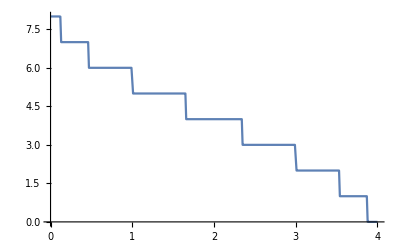

```mathematica
ListPlot[pris,Joined->True]
```

```mathematica
deltae[ω_,ϵ1_]:=Module[{Tin=T[1],μ1=RandomInteger[{1,8}], μ2=RandomInteger[{1,8}], μ3=RandomInteger[{1,8}], μ4=RandomInteger[{1,8}],μ5=RandomInteger[{1,8}], μ6=RandomInteger[{1,8}], μ7=RandomInteger[{1,8}],μ8=RandomInteger[{1,8}], μ9=RandomInteger[{1,8}], μ10=RandomInteger[{1,8}], μ11=RandomInteger[{1,8}],μ12=RandomInteger[{1,8}], μ13=RandomInteger[{1,8}], μ14=RandomInteger[{1,8}]},
imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]];
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]];
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]];
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]];
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]];
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]];
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]];
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]];
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]];
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]];
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]];
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]];
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]];
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]];
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{1,1}}->ω+ⅈ*0.0001-0]]];tra:= Module[{},list={RandomSample[{imp7,imp10,imp9,imp,imp1,imp,imp,imp,imp9,imp9,imp5,imp,imp8,imp11,imp13,imp,imp3,imp3,imp,imp,imp14,imp,imp13,imp8,imp,imp11,imp,imp8,imp7,imp,imp,imp,imp5,imp,imp,imp14,imp,imp5,imp10,imp,imp10,imp2,imp6,imp,imp2,imp11,imp,imp6,imp4,imp,imp,imp,imp,imp6,imp,imp,imp,imp4,imp1,imp,imp10,imp,imp2,imp13,imp,imp4,imp14,imp7,imp,imp11,imp8,imp4,imp7,imp,imp12,imp,imp,imp12,imp14,imp,imp,imp3,imp5,imp,imp1,imp,imp,imp12,imp13,imp2,imp1,imp,imp6,imp12,imp,imp3,imp9,imp,imp,imp}]};b=Module[{},
(*Print[Dimensions[list]];*)sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[8]-list[[1,ζ]].ConjugateTranspose[Tin].J.Tin].list[[1,ζ]],{ζ,1,100}]; J=J];Il1:=Inverse[IdentityMatrix[8]-sl1.Tin.SR[ω,0.0001,1,0].Tin].sl1;
Ir1:=Inverse[IdentityMatrix[8]-SR[ω,0.0001,1,0].Tin.sl1.Tin].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].Tin.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.Tin.grr1.Tin-Tin.GNON1.Tin.GNON1]]>10,10,Abs[Tr[gdd1.Tin.grr1.Tin-Tin.GNON1.Tin.GNON1]]]];
b];
tra]
```

```mathematica
Timing[Mean[Table[deltae[0,0.5],2000]]]
```

{12.2216,1.30238}

```mathematica
Table[{ω,Mean[Table[deltae[ω,0.5],2000]]},{ω,Range[0,4,0.01]}]
Table[{ω,Mean[Table[deltae[ω,0.4],2000]]},{ω,Range[0,4,0.01]}]
Table[{ω,Mean[Table[deltae[ω,0.3],2000]]},{ω,Range[0,4,0.01]}]
Table[{ω,Mean[Table[deltae[ω,0.6],2000]]},{ω,Range[0,4,0.01]}]
Table[{ω,Mean[Table[deltae[ω,0.7],2000]]},{ω,Range[0,4,0.01]}]
Table[{ω,Mean[Table[deltae[ω,0.8],2000]]},{ω,Range[0,4,0.01]}]
Table[{ω,Mean[Table[deltae[ω,0.9],2000]]},{ω,Range[0,4,0.01]}]
```

{{0.,1.26932},{0.01,1.26653},{0.02,1.33451},{0.03,1.34087},{0.04,1.35999},{0.05,1.31072},{0.06,1.35444},{0.07,1.53179},{0.08,1.72158},{0.09,2.22317},{0.1,2.97502},{0.11,4.60245},{0.12,8.13968},{0.13,7.54336},{0.14,6.10182},{0.15,4.20678},{0.16,2.60907},{0.17,1.75118},{0.18,1.61794},{0.19,1.77336},{0.2,1.96626},{0.21,2.17654},{0.22,2.31412},{0.23,2.38053},{0.24,2.45044},{0.25,2.50759},{0.26,2.52625},{0.27,2.57143},{0.28,2.52152},{0.29,2.52615},{0.3,2.48702},{0.31,2.47974},{0.32,2.47409},{0.33,2.3937},{0.34,2.34113},{0.35,2.29869},{0.36,2.23377},{0.37,2.1527},{0.38,2.01996},{0.39,1.85681},{0.4,1.77282},{0.41,1.57165},{0.42,1.39541},{0.43,1.2101},{0.44,1.14486},{0.45,1.35738},{0.46,2.57205},{0.47,6.8802},{0.48,5.4443},{0.49,4.30068},{0.5,3.01068},{0.51,2.07825},{0.52,2.00895},{0.53,2.25236},{0.54,2.58541},{0.55,2.83932},{0.56,2.98399},{0.57,3.10364},{0.58,3.19329},{0.59,3.23499},{0.6,3.27525},{0.61,3.30792},{0.62,3.32168},{0.63,3.34574},{0.64,3.34832},{0.65,3.36445},{0.66,3.38167},{0.67,3.38514},{0.68,3.3688},{0.69,3.37898},{0.7,3.36778},{0.71,3.35145},{0.72,3.35349},{0.73,3.35984},{0.74,3.33952},{0.75,3.31988},{0.76,3.31684},{0.77,3.30418},{0.78,3.26923},{0.79,3.26044},{0.8,3.22627},{0.81,3.19265},{0.82,3.16922},{0.83,3.16135},{0.84,3.11603},{0.85,3.05696},{0.86,2.99202},{0.87,2.95376},{0.88,2.88895},{0.89,2.82374},{0.9,2.73558},{0.91,2.63995},{0.92,2.56117},{0.93,2.40358},{0.94,2.26478},{0.95,2.05342},{0.96,1.78779},{0.97,1.46011},{0.98,1.15988},{0.99,1.27731},{1.,5.48581},{1.01,4.60728},{1.02,3.65053},{1.03,2.90268},{1.04,2.08566},{1.05,1.95002},{1.06,2.35341},{1.07,2.69459},{1.08,2.91502},{1.09,3.05956},{1.1,3.13985},{1.11,3.20004},{1.12,3.24266},{1.13,3.28982},{1.14,3.3057},{1.15,3.3291},{1.16,3.33599},{1.17,3.3327},{1.18,3.34929},{1.19,3.34534},{1.2,3.33305},{1.21,3.35427},{1.22,3.36018},{1.23,3.36653},{1.24,3.35806},{1.25,3.34505},{1.26,3.34039},{1.27,3.33849},{1.28,3.34384},{1.29,3.32758},{1.3,3.32435},{1.31,3.32593},{1.32,3.30363},{1.33,3.30031},{1.34,3.2897},{1.35,3.26923},{1.36,3.27163},{1.37,3.25794},{1.38,3.23388},{1.39,3.22087},{1.4,3.19844},{1.41,3.19215},{1.42,3.17094},{1.43,3.16164},{1.44,3.13744},{1.45,3.11576},{1.46,3.09195},{1.47,3.07565},{1.48,3.0181},{1.49,3.00389},{1.5,2.9638},{1.51,2.92553},{1.52,2.89469},{1.53,2.82721},{1.54,2.76714},{1.55,2.70978},{1.56,2.6405},{1.57,2.55614},{1.58,2.44525},{1.59,2.32491},{1.6,2.19909},{1.61,2.02446},{1.62,1.77333},{1.63,1.41954},{1.64,1.07102},{1.65,1.80924},{1.66,3.83279},{1.67,3.12599},{1.68,2.45094},{1.69,1.83205},{1.7,1.72089},{1.71,1.98977},{1.72,2.36446},{1.73,2.56342},{1.74,2.71311},{1.75,2.76626},{1.76,2.81764},{1.77,2.85026},{1.78,2.85682},{1.79,2.88059},{1.8,2.89259},{1.81,2.90377},{1.82,2.90258},{1.83,2.91383},{1.84,2.91782},{1.85,2.91411},{1.86,2.91385},{1.87,2.92851},{1.88,2.91664},{1.89,2.91812},{1.9,2.91464},{1.91,2.91915},{1.92,2.91135},{1.93,2.90766},{1.94,2.90662},{1.95,2.89981},{1.96,2.8894},{1.97,2.88895},{1.98,2.88443},{1.99,2.87228},{2.,2.86391},{2.01,2.85496},{2.02,2.84921},{2.03,2.84877},{2.04,2.83087},{2.05,2.82404},{2.06,2.82027},{2.07,2.79474},{2.08,2.79046},{2.09,2.77713},{2.1,2.76098},{2.11,2.75342},{2.12,2.723},{2.13,2.71744},{2.14,2.70426},{2.15,2.68307},{2.16,2.66329},{2.17,2.63231},{2.18,2.60686},{2.19,2.5669},{2.2,2.55015},{2.21,2.51494},{2.22,2.48654},{2.23,2.43922},{2.24,2.38907},{2.25,2.33019},{2.26,2.27729},{2.27,2.21762},{2.28,2.15252},{2.29,2.03434},{2.3,1.90911},{2.31,1.74498},{2.32,1.54413},{2.33,1.25013},{2.34,1.01456},{2.35,3.20242},{2.36,2.89753},{2.37,2.39546},{2.38,1.94987},{2.39,1.52422},{2.4,1.51815},{2.41,1.79175},{2.42,2.00528},{2.43,2.1342},{2.44,2.19817},{2.45,2.23557},{2.46,2.25367},{2.47,2.27573},{2.48,2.28502},{2.49,2.28675},{2.5,2.29172},{2.51,2.29583},{2.52,2.295},{2.53,2.29758},{2.54,2.29085},{2.55,2.29177},{2.56,2.30939},{2.57,2.29947},{2.58,2.29035},{2.59,2.29195},{2.6,2.28683},{2.61,2.27861},{2.62,2.27373},{2.63,2.2667},{2.64,2.26447},{2.65,2.24694},{2.66,2.25128},{2.67,2.23691},{2.68,2.23775},{2.69,2.23501},{2.7,2.22577},{2.71,2.20617},{2.72,2.20673},{2.73,2.19693},{2.74,2.19303},{2.75,2.1744},{2.76,2.16034},{2.77,2.14914},{2.78,2.12865},{2.79,2.13131},{2.8,2.10831},{2.81,2.08928},{2.82,2.07506},{2.83,2.06234},{2.84,2.03552},{2.85,2.00437},{2.86,1.98716},{2.87,1.95222},{2.88,1.92919},{2.89,1.8898},{2.9,1.8525},{2.91,1.82347},{2.92,1.76214},{2.93,1.71585},{2.94,1.65296},{2.95,1.57286},{2.96,1.45049},{2.97,1.28102},{2.98,1.12858},{2.99,0.852251},{3.,2.50796},{3.01,2.36119},{3.02,2.02421},{3.03,1.62972},{3.04,1.25656},{3.05,1.01016},{3.06,1.14446},{3.07,1.36422},{3.08,1.45776},{3.09,1.50386},{3.1,1.52161},{3.11,1.52425},{3.12,1.54624},{3.13,1.53719},{3.14,1.5469},{3.15,1.55525},{3.16,1.54955},{3.17,1.55446},{3.18,1.55207},{3.19,1.55085},{3.2,1.54302},{3.21,1.5319},{3.22,1.53686},{3.23,1.52901},{3.24,1.51844},{3.25,1.52155},{3.26,1.51046},{3.27,1.50119},{3.28,1.49181},{3.29,1.48543},{3.3,1.47863},{3.31,1.46002},{3.32,1.45474},{3.33,1.45275},{3.34,1.44401},{3.35,1.41727},{3.36,1.41409},{3.37,1.39874},{3.38,1.36648},{3.39,1.36129},{3.4,1.34674},{3.41,1.3211},{3.42,1.29566},{3.43,1.26587},{3.44,1.24345},{3.45,1.20912},{3.46,1.17797},{3.47,1.12267},{3.48,1.07652},{3.49,1.02225},{3.5,0.939394},{3.51,0.822288},{3.52,0.685992},{3.53,0.73688},{3.54,1.81921},{3.55,1.55194},{3.56,1.32384},{3.57,0.917705},{3.58,0.692325},{3.59,0.583344},{3.6,0.646198},{3.61,0.717724},{3.62,0.750188},{3.63,0.757592},{3.64,0.770442},{3.65,0.766202},{3.66,0.770417},{3.67,0.768929},{3.68,0.762878},{3.69,0.759499},{3.7,0.757975},{3.71,0.751346},{3.72,0.751422},{3.73,0.732342},{3.74,0.723984},{3.75,0.71322},{3.76,0.704061},{3.77,0.690728},{3.78,0.675151},{3.79,0.667644},{3.8,0.638183},{3.81,0.610259},{3.82,0.594859},{3.83,0.557141},{3.84,0.526857},{3.85,0.480765},{3.86,0.41833},{3.87,0.331051},{3.88,0.615479},{3.89,0.594263},{3.9,0.475013},{3.91,0.425628},{3.92,0.214583},{3.93,0.125185},{3.94,0.0282723},{3.95,0.0199302},{3.96,0.00564359},{3.97,0.0042169},{3.98,0.00328014},{3.99,0.00266554},{4.,0.00210215}}

{{0.,1.80543},{0.01,1.85247},{0.02,1.9855},{0.03,2.04676},{0.04,1.89586},{0.05,1.79008},{0.06,1.64773},{0.07,1.61375},{0.08,1.54297},{0.09,1.71736},{0.1,2.21567},{0.11,3.61265},{0.12,7.78235},{0.13,7.11309},{0.14,5.15909},{0.15,3.18507},{0.16,2.16032},{0.17,2.44397},{0.18,2.85089},{0.19,3.14948},{0.2,3.34643},{0.21,3.45889},{0.22,3.50727},{0.23,3.53239},{0.24,3.6013},{0.25,3.60281},{0.26,3.61044},{0.27,3.63886},{0.28,3.60809},{0.29,3.6028},{0.3,3.58485},{0.31,3.55845},{0.32,3.52184},{0.33,3.49214},{0.34,3.42133},{0.35,3.36389},{0.36,3.28018},{0.37,3.18068},{0.38,3.10388},{0.39,2.98598},{0.4,2.80926},{0.41,2.58543},{0.42,2.36941},{0.43,2.02793},{0.44,1.68985},{0.45,1.38392},{0.46,1.954},{0.47,6.47781},{0.48,5.05082},{0.49,3.58674},{0.5,2.53419},{0.51,2.59033},{0.52,3.2396},{0.53,3.59059},{0.54,3.79234},{0.55,3.91279},{0.56,3.96265},{0.57,4.02359},{0.58,4.05661},{0.59,4.07834},{0.6,4.08614},{0.61,4.10484},{0.62,4.12726},{0.63,4.11635},{0.64,4.12793},{0.65,4.14492},{0.66,4.12304},{0.67,4.13273},{0.68,4.1241},{0.69,4.11155},{0.7,4.11475},{0.71,4.09921},{0.72,4.10222},{0.73,4.08152},{0.74,4.06974},{0.75,4.06752},{0.76,4.06097},{0.77,4.03051},{0.78,4.00514},{0.79,3.98071},{0.8,3.9981},{0.81,3.95173},{0.82,3.91073},{0.83,3.89351},{0.84,3.84669},{0.85,3.80624},{0.86,3.77498},{0.87,3.73157},{0.88,3.67447},{0.89,3.61127},{0.9,3.5509},{0.91,3.43759},{0.92,3.32869},{0.93,3.22271},{0.94,3.07424},{0.95,2.89167},{0.96,2.62147},{0.97,2.29406},{0.98,1.81671},{0.99,1.32132},{1.,5.05522},{1.01,4.29645},{1.02,3.12982},{1.03,2.48676},{1.04,2.49251},{1.05,3.12458},{1.06,3.46726},{1.07,3.63041},{1.08,3.69586},{1.09,3.76523},{1.1,3.77939},{1.11,3.8126},{1.12,3.82523},{1.13,3.84365},{1.14,3.85229},{1.15,3.85109},{1.16,3.87348},{1.17,3.86093},{1.18,3.86654},{1.19,3.86969},{1.2,3.86755},{1.21,3.86995},{1.22,3.87199},{1.23,3.85973},{1.24,3.85429},{1.25,3.85843},{1.26,3.85096},{1.27,3.84954},{1.28,3.84314},{1.29,3.84034},{1.3,3.83662},{1.31,3.8241},{1.32,3.81519},{1.33,3.80584},{1.34,3.8051},{1.35,3.79041},{1.36,3.77753},{1.37,3.76826},{1.38,3.75779},{1.39,3.73994},{1.4,3.73113},{1.41,3.71815},{1.42,3.69843},{1.43,3.688},{1.44,3.668},{1.45,3.64127},{1.46,3.62276},{1.47,3.61418},{1.48,3.57064},{1.49,3.54969},{1.5,3.51776},{1.51,3.47886},{1.52,3.44136},{1.53,3.41289},{1.54,3.35861},{1.55,3.28952},{1.56,3.23965},{1.57,3.15511},{1.58,3.06655},{1.59,2.96152},{1.6,2.85144},{1.61,2.66199},{1.62,2.4507},{1.63,2.09335},{1.64,1.55028},{1.65,1.60204},{1.66,3.62451},{1.67,2.96111},{1.68,2.17618},{1.69,2.11023},{1.7,2.57324},{1.71,2.9429},{1.72,3.09276},{1.73,3.15906},{1.74,3.2081},{1.75,3.22486},{1.76,3.24647},{1.77,3.25461},{1.78,3.259},{1.79,3.27573},{1.8,3.26668},{1.81,3.28198},{1.82,3.28046},{1.83,3.28478},{1.84,3.28521},{1.85,3.29086},{1.86,3.28051},{1.87,3.28221},{1.88,3.28005},{1.89,3.27867},{1.9,3.27329},{1.91,3.27319},{1.92,3.27015},{1.93,3.26659},{1.94,3.26732},{1.95,3.25626},{1.96,3.25632},{1.97,3.24656},{1.98,3.22677},{1.99,3.24517},{2.,3.2274},{2.01,3.22084},{2.02,3.21382},{2.03,3.20749},{2.04,3.20398},{2.05,3.18235},{2.06,3.17934},{2.07,3.17911},{2.08,3.16692},{2.09,3.15656},{2.1,3.14159},{2.11,3.12412},{2.12,3.11764},{2.13,3.10052},{2.14,3.08118},{2.15,3.06416},{2.16,3.05406},{2.17,3.02975},{2.18,3.0088},{2.19,2.98727},{2.2,2.96845},{2.21,2.93787},{2.22,2.91079},{2.23,2.87591},{2.24,2.84309},{2.25,2.80033},{2.26,2.74151},{2.27,2.67152},{2.28,2.60587},{2.29,2.53534},{2.3,2.40682},{2.31,2.25693},{2.32,2.06297},{2.33,1.72126},{2.34,1.20402},{2.35,3.26535},{2.36,2.74614},{2.37,2.1787},{2.38,1.71122},{2.39,1.91696},{2.4,2.23287},{2.41,2.41233},{2.42,2.47903},{2.43,2.49633},{2.44,2.51905},{2.45,2.52162},{2.46,2.533},{2.47,2.54084},{2.48,2.54219},{2.49,2.54902},{2.5,2.54765},{2.51,2.54738},{2.52,2.54141},{2.53,2.5487},{2.54,2.54349},{2.55,2.54405},{2.56,2.53794},{2.57,2.53395},{2.58,2.5309},{2.59,2.53254},{2.6,2.52629},{2.61,2.51574},{2.62,2.51876},{2.63,2.51465},{2.64,2.50697},{2.65,2.50821},{2.66,2.48876},{2.67,2.49482},{2.68,2.48757},{2.69,2.4811},{2.7,2.46919},{2.71,2.46988},{2.72,2.4624},{2.73,2.44727},{2.74,2.42898},{2.75,2.43426},{2.76,2.41784},{2.77,2.40514},{2.78,2.40166},{2.79,2.38231},{2.8,2.37309},{2.81,2.37022},{2.82,2.35445},{2.83,2.32653},{2.84,2.31956},{2.85,2.29453},{2.86,2.28117},{2.87,2.25764},{2.88,2.22354},{2.89,2.20303},{2.9,2.16449},{2.91,2.13915},{2.92,2.09719},{2.93,2.04247},{2.94,1.977},{2.95,1.91369},{2.96,1.81749},{2.97,1.69196},{2.98,1.47629},{2.99,1.17144},{3.,2.44704},{3.01,2.29353},{3.02,1.97564},{3.03,1.38456},{3.04,1.17496},{3.05,1.47873},{3.06,1.63024},{3.07,1.66784},{3.08,1.69146},{3.09,1.69923},{3.1,1.71092},{3.11,1.71408},{3.12,1.71175},{3.13,1.71854},{3.14,1.71637},{3.15,1.71172},{3.16,1.70998},{3.17,1.71384},{3.18,1.70619},{3.19,1.70788},{3.2,1.70268},{3.21,1.69053},{3.22,1.69461},{3.23,1.6842},{3.24,1.68698},{3.25,1.68472},{3.26,1.67663},{3.27,1.66747},{3.28,1.65609},{3.29,1.65224},{3.3,1.64755},{3.31,1.63317},{3.32,1.63018},{3.33,1.63083},{3.34,1.61443},{3.35,1.60177},{3.36,1.591},{3.37,1.57234},{3.38,1.55598},{3.39,1.55267},{3.4,1.53315},{3.41,1.51914},{3.42,1.49895},{3.43,1.48054},{3.44,1.45824},{3.45,1.4171},{3.46,1.3876},{3.47,1.35425},{3.48,1.3047},{3.49,1.24385},{3.5,1.17787},{3.51,1.03909},{3.52,0.883164},{3.53,0.708745},{3.54,1.69446},{3.55,1.45766},{3.56,1.06862},{3.57,0.744279},{3.58,0.716848},{3.59,0.806267},{3.6,0.845309},{3.61,0.849992},{3.62,0.858095},{3.63,0.860035},{3.64,0.861679},{3.65,0.856827},{3.66,0.861706},{3.67,0.860596},{3.68,0.845328},{3.69,0.844082},{3.7,0.840135},{3.71,0.835061},{3.72,0.828423},{3.73,0.827027},{3.74,0.82122},{3.75,0.806127},{3.76,0.786741},{3.77,0.786375},{3.78,0.776845},{3.79,0.76444},{3.8,0.745653},{3.81,0.723056},{3.82,0.7019},{3.83,0.670486},{3.84,0.63195},{3.85,0.588416},{3.86,0.539643},{3.87,0.420652},{3.88,0.603196},{3.89,0.499996},{3.9,0.363678},{3.91,0.261486},{3.92,0.0753903},{3.93,0.0248536},{3.94,0.00528978},{3.95,0.00339636},{3.96,0.00266697},{3.97,0.00199331},{3.98,0.00162816},{3.99,0.00135792},{4.,0.00111433}}

{{0.,3.17319},{0.01,3.24192},{0.02,3.42178},{0.03,3.33787},{0.04,3.13567},{0.05,3.0205},{0.06,2.85638},{0.07,2.63655},{0.08,2.41448},{0.09,2.11874},{0.1,2.01058},{0.11,2.5794},{0.12,7.10862},{0.13,6.41388},{0.14,3.95204},{0.15,2.98519},{0.16,3.81881},{0.17,4.26685},{0.18,4.4841},{0.19,4.60667},{0.2,4.69463},{0.21,4.72417},{0.22,4.77795},{0.23,4.78362},{0.24,4.79413},{0.25,4.80671},{0.26,4.79919},{0.27,4.79063},{0.28,4.75558},{0.29,4.77341},{0.3,4.73105},{0.31,4.70133},{0.32,4.67428},{0.33,4.66788},{0.34,4.56482},{0.35,4.55464},{0.36,4.48521},{0.37,4.3966},{0.38,4.31134},{0.39,4.16923},{0.4,4.04447},{0.41,3.91412},{0.42,3.66169},{0.43,3.33132},{0.44,2.88487},{0.45,2.21502},{0.46,1.67249},{0.47,6.26302},{0.48,4.65742},{0.49,2.96773},{0.5,3.56842},{0.51,4.31653},{0.52,4.57586},{0.53,4.6911},{0.54,4.74872},{0.55,4.77681},{0.56,4.80243},{0.57,4.81826},{0.58,4.83215},{0.59,4.84068},{0.6,4.83816},{0.61,4.85172},{0.62,4.85455},{0.63,4.84537},{0.64,4.85404},{0.65,4.84873},{0.66,4.84439},{0.67,4.84245},{0.68,4.84507},{0.69,4.84048},{0.7,4.83753},{0.71,4.81874},{0.72,4.81816},{0.73,4.80346},{0.74,4.80011},{0.75,4.78226},{0.76,4.78222},{0.77,4.76219},{0.78,4.76384},{0.79,4.73744},{0.8,4.7196},{0.81,4.70213},{0.82,4.67267},{0.83,4.65109},{0.84,4.61642},{0.85,4.58716},{0.86,4.54839},{0.87,4.52037},{0.88,4.48383},{0.89,4.4133},{0.9,4.37879},{0.91,4.29308},{0.92,4.22289},{0.93,4.12162},{0.94,4.01102},{0.95,3.85999},{0.96,3.62235},{0.97,3.34739},{0.98,2.82252},{0.99,1.94871},{1.,5.04232},{1.01,4.10994},{1.02,2.9143},{1.03,3.16588},{1.04,3.94619},{1.05,4.1515},{1.06,4.22085},{1.07,4.2591},{1.08,4.28759},{1.09,4.29858},{1.1,4.30868},{1.11,4.31715},{1.12,4.32242},{1.13,4.32837},{1.14,4.33421},{1.15,4.32981},{1.16,4.33051},{1.17,4.3309},{1.18,4.32813},{1.19,4.33014},{1.2,4.32454},{1.21,4.33158},{1.22,4.32565},{1.23,4.32439},{1.24,4.31729},{1.25,4.31712},{1.26,4.30812},{1.27,4.30193},{1.28,4.2993},{1.29,4.30232},{1.3,4.29653},{1.31,4.29286},{1.32,4.28095},{1.33,4.2845},{1.34,4.27429},{1.35,4.26632},{1.36,4.26227},{1.37,4.24643},{1.38,4.23673},{1.39,4.23568},{1.4,4.22321},{1.41,4.21223},{1.42,4.19667},{1.43,4.18242},{1.44,4.16869},{1.45,4.1586},{1.46,4.14432},{1.47,4.12182},{1.48,4.11552},{1.49,4.08849},{1.5,4.06235},{1.51,4.0381},{1.52,4.01915},{1.53,3.97778},{1.54,3.93496},{1.55,3.89156},{1.56,3.84809},{1.57,3.79743},{1.58,3.71736},{1.59,3.63523},{1.6,3.53712},{1.61,3.37639},{1.62,3.19413},{1.63,2.85382},{1.64,2.3047},{1.65,1.43299},{1.66,3.62697},{1.67,2.62498},{1.68,2.50395},{1.69,3.20493},{1.7,3.44935},{1.71,3.51027},{1.72,3.53882},{1.73,3.55703},{1.74,3.5667},{1.75,3.57375},{1.76,3.582},{1.77,3.58684},{1.78,3.58705},{1.79,3.59188},{1.8,3.59251},{1.81,3.58836},{1.82,3.59114},{1.83,3.58749},{1.84,3.59244},{1.85,3.58704},{1.86,3.58969},{1.87,3.58576},{1.88,3.58403},{1.89,3.58116},{1.9,3.57767},{1.91,3.57415},{1.92,3.57429},{1.93,3.57074},{1.94,3.56449},{1.95,3.56663},{1.96,3.56847},{1.97,3.55929},{1.98,3.55409},{1.99,3.55019},{2.,3.54809},{2.01,3.53954},{2.02,3.54205},{2.03,3.52862},{2.04,3.52044},{2.05,3.52435},{2.06,3.51529},{2.07,3.51008},{2.08,3.49958},{2.09,3.49299},{2.1,3.48453},{2.11,3.47791},{2.12,3.46672},{2.13,3.45746},{2.14,3.44601},{2.15,3.43823},{2.16,3.42524},{2.17,3.40641},{2.18,3.38842},{2.19,3.37587},{2.2,3.3538},{2.21,3.3378},{2.22,3.3035},{2.23,3.28682},{2.24,3.2688},{2.25,3.23282},{2.26,3.18615},{2.27,3.13889},{2.28,3.09691},{2.29,3.01399},{2.3,2.94765},{2.31,2.79926},{2.32,2.64629},{2.33,2.33619},{2.34,1.69766},{2.35,3.25075},{2.36,2.63026},{2.37,1.98006},{2.38,2.30793},{2.39,2.61879},{2.4,2.68966},{2.41,2.71936},{2.42,2.7287},{2.43,2.73127},{2.44,2.73511},{2.45,2.74592},{2.46,2.74143},{2.47,2.7443},{2.48,2.74807},{2.49,2.74552},{2.5,2.74244},{2.51,2.74074},{2.52,2.74204},{2.53,2.73786},{2.54,2.73609},{2.55,2.73937},{2.56,2.73119},{2.57,2.72959},{2.58,2.73219},{2.59,2.72988},{2.6,2.72794},{2.61,2.72353},{2.62,2.71872},{2.63,2.71624},{2.64,2.71154},{2.65,2.70995},{2.66,2.70395},{2.67,2.70241},{2.68,2.70057},{2.69,2.6986},{2.7,2.69034},{2.71,2.68448},{2.72,2.68115},{2.73,2.67},{2.74,2.6735},{2.75,2.66711},{2.76,2.66092},{2.77,2.65036},{2.78,2.64159},{2.79,2.62835},{2.8,2.62578},{2.81,2.6178},{2.82,2.61125},{2.83,2.59479},{2.84,2.58446},{2.85,2.56829},{2.86,2.55243},{2.87,2.5412},{2.88,2.52888},{2.89,2.49968},{2.9,2.47531},{2.91,2.46253},{2.92,2.41688},{2.93,2.37055},{2.94,2.33573},{2.95,2.2823},{2.96,2.20127},{2.97,2.08286},{2.98,1.9199},{2.99,1.57751},{3.,2.56037},{3.01,2.24368},{3.02,1.61026},{3.03,1.44943},{3.04,1.74912},{3.05,1.80786},{3.06,1.8233},{3.07,1.83402},{3.08,1.83633},{3.09,1.84406},{3.1,1.84318},{3.11,1.84257},{3.12,1.84094},{3.13,1.8458},{3.14,1.83869},{3.15,1.84092},{3.16,1.83628},{3.17,1.83532},{3.18,1.8306},{3.19,1.8297},{3.2,1.82854},{3.21,1.82553},{3.22,1.81935},{3.23,1.81956},{3.24,1.81556},{3.25,1.81253},{3.26,1.80815},{3.27,1.8065},{3.28,1.80479},{3.29,1.79802},{3.3,1.79211},{3.31,1.78811},{3.32,1.7844},{3.33,1.77384},{3.34,1.77125},{3.35,1.76388},{3.36,1.75526},{3.37,1.74546},{3.38,1.73683},{3.39,1.73175},{3.4,1.71432},{3.41,1.69918},{3.42,1.68884},{3.43,1.67009},{3.44,1.65547},{3.45,1.62925},{3.46,1.6138},{3.47,1.56801},{3.48,1.53427},{3.49,1.49033},{3.5,1.41863},{3.51,1.32411},{3.52,1.14873},{3.53,0.750591},{3.54,1.64039},{3.55,1.18419},{3.56,0.773591},{3.57,0.851828},{3.58,0.904542},{3.59,0.918715},{3.6,0.921989},{3.61,0.925321},{3.62,0.923934},{3.63,0.925222},{3.64,0.922787},{3.65,0.921601},{3.66,0.919199},{3.67,0.915965},{3.68,0.91554},{3.69,0.909025},{3.7,0.905225},{3.71,0.907965},{3.72,0.8996},{3.73,0.897222},{3.74,0.890275},{3.75,0.886914},{3.76,0.875269},{3.77,0.871427},{3.78,0.863782},{3.79,0.852945},{3.8,0.840669},{3.81,0.826769},{3.82,0.809634},{3.83,0.781231},{3.84,0.761013},{3.85,0.707945},{3.86,0.650312},{3.87,0.549176},{3.88,0.439375},{3.89,0.316564},{3.9,0.152075},{3.91,0.0382803},{3.92,0.00522248},{3.93,0.00296033},{3.94,0.00198997},{3.95,0.00149261},{3.96,0.00111455},{3.97,0.00094439},{3.98,0.000758995},{3.99,0.000598296},{4.,0.000529375}}

{{0.,1.4616},{0.01,1.54349},{0.02,1.46434},{0.03,1.44723},{0.04,1.52244},{0.05,1.59725},{0.06,1.71894},{0.07,2.03826},{0.08,2.3274},{0.09,3.03983},{0.1,3.86681},{0.11,5.45602},{0.12,8.4668},{0.13,7.816},{0.14,6.58292},{0.15,5.10282},{0.16,3.58193},{0.17,2.34941},{0.18,1.60406},{0.19,1.20115},{0.2,1.14914},{0.21,1.18267},{0.22,1.26532},{0.23,1.37099},{0.24,1.44687},{0.25,1.48328},{0.26,1.56601},{0.27,1.59888},{0.28,1.60564},{0.29,1.61617},{0.3,1.60327},{0.31,1.61716},{0.32,1.52743},{0.33,1.512},{0.34,1.4575},{0.35,1.42227},{0.36,1.33147},{0.37,1.29374},{0.38,1.2035},{0.39,1.11142},{0.4,1.0323},{0.41,0.988287},{0.42,0.965609},{0.43,1.01336},{0.44,1.23828},{0.45,1.78438},{0.46,3.48705},{0.47,7.08926},{0.48,5.89432},{0.49,4.75937},{0.5,3.56658},{0.51,2.58576},{0.52,1.8998},{0.53,1.52209},{0.54,1.62912},{0.55,1.80584},{0.56,2.02211},{0.57,2.16155},{0.58,2.29073},{0.59,2.35203},{0.6,2.44306},{0.61,2.48225},{0.62,2.53237},{0.63,2.58193},{0.64,2.59068},{0.65,2.6214},{0.66,2.60822},{0.67,2.63469},{0.68,2.65054},{0.69,2.65539},{0.7,2.67365},{0.71,2.6606},{0.72,2.64985},{0.73,2.63483},{0.74,2.62684},{0.75,2.62015},{0.76,2.62608},{0.77,2.60525},{0.78,2.57656},{0.79,2.56289},{0.8,2.54728},{0.81,2.52716},{0.82,2.49127},{0.83,2.44024},{0.84,2.42253},{0.85,2.36342},{0.86,2.30329},{0.87,2.24922},{0.88,2.19316},{0.89,2.10869},{0.9,2.04328},{0.91,1.93304},{0.92,1.84915},{0.93,1.7055},{0.94,1.51916},{0.95,1.32279},{0.96,1.12207},{0.97,0.997594},{0.98,0.982856},{0.99,1.57233},{1.,5.50568},{1.01,4.69739},{1.02,4.03768},{1.03,3.19238},{1.04,2.42603},{1.05,1.85851},{1.06,1.60747},{1.07,1.72037},{1.08,1.95872},{1.09,2.2171},{1.1,2.37562},{1.11,2.50742},{1.12,2.58332},{1.13,2.62733},{1.14,2.68645},{1.15,2.72507},{1.16,2.75639},{1.17,2.76415},{1.18,2.77778},{1.19,2.79089},{1.2,2.80993},{1.21,2.81426},{1.22,2.83368},{1.23,2.84526},{1.24,2.83117},{1.25,2.83999},{1.26,2.81773},{1.27,2.80781},{1.28,2.81978},{1.29,2.80321},{1.3,2.80251},{1.31,2.79907},{1.32,2.80674},{1.33,2.79235},{1.34,2.78067},{1.35,2.76316},{1.36,2.75629},{1.37,2.73008},{1.38,2.73329},{1.39,2.71456},{1.4,2.70828},{1.41,2.69928},{1.42,2.65077},{1.43,2.63872},{1.44,2.61411},{1.45,2.59518},{1.46,2.55824},{1.47,2.52848},{1.48,2.50379},{1.49,2.46792},{1.5,2.41623},{1.51,2.38313},{1.52,2.32508},{1.53,2.28948},{1.54,2.21924},{1.55,2.18267},{1.56,2.09886},{1.57,2.01002},{1.58,1.89341},{1.59,1.78323},{1.6,1.61813},{1.61,1.44782},{1.62,1.19106},{1.63,0.988728},{1.64,0.953357},{1.65,2.27069},{1.66,4.01088},{1.67,3.25456},{1.68,2.64157},{1.69,2.17098},{1.7,1.60384},{1.71,1.4553},{1.72,1.54263},{1.73,1.79232},{1.74,2.01014},{1.75,2.15985},{1.76,2.28612},{1.77,2.35615},{1.78,2.39114},{1.79,2.42983},{1.8,2.44956},{1.81,2.46939},{1.82,2.48824},{1.83,2.50981},{1.84,2.50417},{1.85,2.51485},{1.86,2.52691},{1.87,2.52787},{1.88,2.53925},{1.89,2.53118},{1.9,2.53017},{1.91,2.54986},{1.92,2.52655},{1.93,2.52536},{1.94,2.53504},{1.95,2.51484},{1.96,2.51315},{1.97,2.51192},{1.98,2.50199},{1.99,2.48208},{2.,2.48215},{2.01,2.47338},{2.02,2.47561},{2.03,2.4615},{2.04,2.45774},{2.05,2.4526},{2.06,2.43572},{2.07,2.41707},{2.08,2.40588},{2.09,2.39542},{2.1,2.38055},{2.11,2.35738},{2.12,2.33348},{2.13,2.31636},{2.14,2.30489},{2.15,2.27653},{2.16,2.26535},{2.17,2.24506},{2.18,2.22464},{2.19,2.18048},{2.2,2.13095},{2.21,2.10785},{2.22,2.07196},{2.23,2.02699},{2.24,1.97035},{2.25,1.91147},{2.26,1.86065},{2.27,1.76634},{2.28,1.69607},{2.29,1.58432},{2.3,1.4603},{2.31,1.30509},{2.32,1.1022},{2.33,0.885791},{2.34,0.975827},{2.35,3.34251},{2.36,2.76506},{2.37,2.58176},{2.38,2.09689},{2.39,1.67778},{2.4,1.36643},{2.41,1.25751},{2.42,1.35635},{2.43,1.57303},{2.44,1.7265},{2.45,1.83041},{2.46,1.90171},{2.47,1.93834},{2.48,1.96919},{2.49,1.98593},{2.5,1.99868},{2.51,2.00337},{2.52,2.01901},{2.53,2.01715},{2.54,2.02568},{2.55,2.02774},{2.56,2.03216},{2.57,2.02717},{2.58,2.01923},{2.59,2.0284},{2.6,2.02525},{2.61,2.02288},{2.62,2.00697},{2.63,2.00055},{2.64,1.9982},{2.65,2.00063},{2.66,1.99001},{2.67,1.98428},{2.68,1.98422},{2.69,1.95979},{2.7,1.9515},{2.71,1.93622},{2.72,1.93148},{2.73,1.92205},{2.74,1.89749},{2.75,1.89881},{2.76,1.8865},{2.77,1.86819},{2.78,1.85775},{2.79,1.84398},{2.8,1.8161},{2.81,1.81746},{2.82,1.78954},{2.83,1.75928},{2.84,1.74745},{2.85,1.72225},{2.86,1.67574},{2.87,1.66676},{2.88,1.63222},{2.89,1.57372},{2.9,1.56458},{2.91,1.49363},{2.92,1.44841},{2.93,1.40307},{2.94,1.32207},{2.95,1.25388},{2.96,1.14144},{2.97,0.995254},{2.98,0.836758},{2.99,0.727967},{3.,2.56026},{3.01,2.40247},{3.02,2.17029},{3.03,1.76906},{3.04,1.46754},{3.05,1.15408},{3.06,0.896221},{3.07,0.887217},{3.08,1.0467},{3.09,1.17858},{3.1,1.2556},{3.11,1.28991},{3.12,1.32629},{3.13,1.35231},{3.14,1.36701},{3.15,1.362},{3.16,1.35965},{3.17,1.37715},{3.18,1.36984},{3.19,1.36372},{3.2,1.35911},{3.21,1.3598},{3.22,1.36268},{3.23,1.35127},{3.24,1.356},{3.25,1.34563},{3.26,1.33512},{3.27,1.3191},{3.28,1.31357},{3.29,1.30817},{3.3,1.30195},{3.31,1.27912},{3.32,1.27282},{3.33,1.26066},{3.34,1.24799},{3.35,1.2343},{3.36,1.22467},{3.37,1.20825},{3.38,1.17975},{3.39,1.16518},{3.4,1.14741},{3.41,1.12606},{3.42,1.0928},{3.43,1.0754},{3.44,1.04607},{3.45,1.0206},{3.46,0.976746},{3.47,0.923969},{3.48,0.86308},{3.49,0.799676},{3.5,0.732999},{3.51,0.644852},{3.52,0.548705},{3.53,0.773745},{3.54,1.7711},{3.55,1.60964},{3.56,1.48188},{3.57,1.21721},{3.58,0.957345},{3.59,0.638806},{3.6,0.52106},{3.61,0.49818},{3.62,0.558676},{3.63,0.596029},{3.64,0.635323},{3.65,0.647779},{3.66,0.661024},{3.67,0.668553},{3.68,0.67149},{3.69,0.657291},{3.7,0.66012},{3.71,0.648021},{3.72,0.653061},{3.73,0.63656},{3.74,0.622871},{3.75,0.624731},{3.76,0.605594},{3.77,0.590093},{3.78,0.580536},{3.79,0.554663},{3.8,0.543447},{3.81,0.518928},{3.82,0.479315},{3.83,0.460121},{3.84,0.412755},{3.85,0.375721},{3.86,0.318498},{3.87,0.260611},{3.88,0.762308},{3.89,0.719336},{3.9,0.675701},{3.91,0.51852},{3.92,0.354614},{3.93,0.248089},{3.94,0.16604},{3.95,0.0753276},{3.96,0.0386575},{3.97,0.00997005},{3.98,0.00714044},{3.99,0.00506565},{4.,0.00380888}}

{{0.,2.08928},{0.01,2.02051},{0.02,1.94626},{0.03,1.8942},{0.04,2.04643},{0.05,2.09711},{0.06,2.3078},{0.07,2.68309},{0.08,3.06255},{0.09,3.659},{0.1,4.55561},{0.11,6.20113},{0.12,8.6639},{0.13,7.89211},{0.14,6.92024},{0.15,5.80367},{0.16,4.3344},{0.17,3.26143},{0.18,2.33105},{0.19,1.67202},{0.2,1.25125},{0.21,1.04079},{0.22,0.869608},{0.23,0.854941},{0.24,0.85882},{0.25,0.871722},{0.26,0.891353},{0.27,0.926434},{0.28,0.915065},{0.29,0.936396},{0.3,0.954668},{0.31,0.955379},{0.32,0.908457},{0.33,0.913644},{0.34,0.90775},{0.35,0.863133},{0.36,0.861641},{0.37,0.803099},{0.38,0.798828},{0.39,0.814604},{0.4,0.81854},{0.41,0.891886},{0.42,0.980006},{0.43,1.20653},{0.44,1.66184},{0.45,2.50375},{0.46,3.97178},{0.47,7.30294},{0.48,6.21958},{0.49,5.32068},{0.5,4.14903},{0.51,3.29507},{0.52,2.32181},{0.53,1.74615},{0.54,1.33427},{0.55,1.20964},{0.56,1.24577},{0.57,1.37355},{0.58,1.46758},{0.59,1.57397},{0.6,1.65992},{0.61,1.73137},{0.62,1.78569},{0.63,1.85323},{0.64,1.90716},{0.65,1.93359},{0.66,1.9554},{0.67,1.98276},{0.68,2.00539},{0.69,1.99446},{0.7,1.99578},{0.71,1.99681},{0.72,1.99415},{0.73,1.99786},{0.74,1.98589},{0.75,1.95966},{0.76,1.98802},{0.77,1.97773},{0.78,1.95993},{0.79,1.93747},{0.8,1.89259},{0.81,1.90291},{0.82,1.86764},{0.83,1.81034},{0.84,1.79317},{0.85,1.75623},{0.86,1.68463},{0.87,1.64134},{0.88,1.567},{0.89,1.49815},{0.9,1.40713},{0.91,1.3203},{0.92,1.25148},{0.93,1.12017},{0.94,0.996772},{0.95,0.91627},{0.96,0.81},{0.97,0.839536},{0.98,1.13378},{0.99,2.0215},{1.,6.09035},{1.01,5.07005},{1.02,4.34591},{1.03,3.5356},{1.04,2.86153},{1.05,2.09266},{1.06,1.56806},{1.07,1.3717},{1.08,1.30854},{1.09,1.40154},{1.1,1.58891},{1.11,1.74725},{1.12,1.86974},{1.13,1.97725},{1.14,2.05994},{1.15,2.10149},{1.16,2.17471},{1.17,2.20618},{1.18,2.23053},{1.19,2.25225},{1.2,2.25414},{1.21,2.28917},{1.22,2.29894},{1.23,2.3182},{1.24,2.32137},{1.25,2.32997},{1.26,2.33148},{1.27,2.31814},{1.28,2.32535},{1.29,2.33268},{1.3,2.31658},{1.31,2.31173},{1.32,2.30177},{1.33,2.30388},{1.34,2.29014},{1.35,2.28813},{1.36,2.27058},{1.37,2.2468},{1.38,2.24927},{1.39,2.22053},{1.4,2.20328},{1.41,2.19434},{1.42,2.1745},{1.43,2.15899},{1.44,2.12605},{1.45,2.11081},{1.46,2.06318},{1.47,2.05309},{1.48,2.02657},{1.49,2.0063},{1.5,1.9664},{1.51,1.88369},{1.52,1.8707},{1.53,1.81275},{1.54,1.74889},{1.55,1.65668},{1.56,1.60861},{1.57,1.50364},{1.58,1.40483},{1.59,1.28257},{1.6,1.14126},{1.61,0.994827},{1.62,0.837594},{1.63,0.768784},{1.64,1.00047},{1.65,2.53814},{1.66,4.09205},{1.67,3.42949},{1.68,3.06413},{1.69,2.48559},{1.7,1.96573},{1.71,1.53127},{1.72,1.32333},{1.73,1.20671},{1.74,1.32893},{1.75,1.52322},{1.76,1.66157},{1.77,1.77967},{1.78,1.87394},{1.79,1.93835},{1.8,1.98737},{1.81,2.0256},{1.82,2.04321},{1.83,2.07964},{1.84,2.09552},{1.85,2.11091},{1.86,2.12054},{1.87,2.11679},{1.88,2.1411},{1.89,2.13353},{1.9,2.14115},{1.91,2.14205},{1.92,2.13009},{1.93,2.14703},{1.94,2.14952},{1.95,2.13419},{1.96,2.12803},{1.97,2.13245},{1.98,2.14063},{1.99,2.1326},{2.,2.12094},{2.01,2.10001},{2.02,2.0933},{2.03,2.09611},{2.04,2.07252},{2.05,2.07068},{2.06,2.07143},{2.07,2.04977},{2.08,2.03374},{2.09,2.01351},{2.1,2.00364},{2.11,1.98275},{2.12,1.97741},{2.13,1.94146},{2.14,1.91976},{2.15,1.90458},{2.16,1.87912},{2.17,1.84635},{2.18,1.81384},{2.19,1.8035},{2.2,1.75045},{2.21,1.73786},{2.22,1.68222},{2.23,1.65141},{2.24,1.58609},{2.25,1.53967},{2.26,1.48013},{2.27,1.40163},{2.28,1.30931},{2.29,1.21501},{2.3,1.09256},{2.31,0.931885},{2.32,0.779633},{2.33,0.740714},{2.34,1.07485},{2.35,3.47973},{2.36,3.02369},{2.37,2.69601},{2.38,2.32235},{2.39,1.84006},{2.4,1.52675},{2.41,1.26535},{2.42,1.08912},{2.43,1.09002},{2.44,1.15812},{2.45,1.31215},{2.46,1.42688},{2.47,1.53494},{2.48,1.59746},{2.49,1.64173},{2.5,1.67209},{2.51,1.68701},{2.52,1.71183},{2.53,1.72038},{2.54,1.71154},{2.55,1.7319},{2.56,1.73111},{2.57,1.73626},{2.58,1.75557},{2.59,1.75105},{2.6,1.74436},{2.61,1.75396},{2.62,1.73491},{2.63,1.7354},{2.64,1.72203},{2.65,1.71475},{2.66,1.72651},{2.67,1.70819},{2.68,1.69128},{2.69,1.68525},{2.7,1.68206},{2.71,1.67785},{2.72,1.66862},{2.73,1.65577},{2.74,1.64246},{2.75,1.62256},{2.76,1.61721},{2.77,1.60214},{2.78,1.59005},{2.79,1.56021},{2.8,1.56591},{2.81,1.51627},{2.82,1.5231},{2.83,1.48577},{2.84,1.44582},{2.85,1.44357},{2.86,1.41665},{2.87,1.38711},{2.88,1.33868},{2.89,1.3002},{2.9,1.27547},{2.91,1.2226},{2.92,1.16715},{2.93,1.10382},{2.94,1.03282},{2.95,0.965691},{2.96,0.847346},{2.97,0.741754},{2.98,0.659454},{2.99,0.681994},{3.,2.67842},{3.01,2.58182},{3.02,2.23084},{3.03,1.97975},{3.04,1.76928},{3.05,1.35414},{3.06,1.0984},{3.07,0.891291},{3.08,0.732455},{3.09,0.784866},{3.1,0.88735},{3.11,0.974741},{3.12,1.05864},{3.13,1.09004},{3.14,1.13151},{3.15,1.13674},{3.16,1.15402},{3.17,1.16673},{3.18,1.17584},{3.19,1.17345},{3.2,1.16639},{3.21,1.17058},{3.22,1.1607},{3.23,1.15514},{3.24,1.15535},{3.25,1.15946},{3.26,1.14372},{3.27,1.13854},{3.28,1.11855},{3.29,1.11764},{3.3,1.12248},{3.31,1.09342},{3.32,1.09071},{3.33,1.0708},{3.34,1.05635},{3.35,1.0466},{3.36,1.0421},{3.37,1.01629},{3.38,0.99848},{3.39,0.961984},{3.4,0.95536},{3.41,0.937419},{3.42,0.8985},{3.43,0.876889},{3.44,0.850185},{3.45,0.812024},{3.46,0.793972},{3.47,0.733426},{3.48,0.672987},{3.49,0.637629},{3.5,0.574324},{3.51,0.50349},{3.52,0.484188},{3.53,0.837341},{3.54,1.91582},{3.55,1.73945},{3.56,1.54206},{3.57,1.31285},{3.58,1.20749},{3.59,0.871959},{3.6,0.617274},{3.61,0.505518},{3.62,0.443361},{3.63,0.422525},{3.64,0.462524},{3.65,0.490334},{3.66,0.514997},{3.67,0.528306},{3.68,0.541434},{3.69,0.546333},{3.7,0.542442},{3.71,0.546584},{3.72,0.545292},{3.73,0.532481},{3.74,0.520837},{3.75,0.515851},{3.76,0.506108},{3.77,0.494257},{3.78,0.484451},{3.79,0.45572},{3.8,0.448675},{3.81,0.416572},{3.82,0.404178},{3.83,0.361741},{3.84,0.32961},{3.85,0.296694},{3.86,0.264601},{3.87,0.231894},{3.88,0.877629},{3.89,0.68374},{3.9,0.706},{3.91,0.550446},{3.92,0.536419},{3.93,0.430513},{3.94,0.264809},{3.95,0.193698},{3.96,0.134892},{3.97,0.0740468},{3.98,0.0357644},{3.99,0.0220382},{4.,0.00781073}}

{{0.,2.62295},{0.01,2.58244},{0.02,2.54736},{0.03,2.5266},{0.04,2.59311},{0.05,2.66626},{0.06,2.90393},{0.07,3.37028},{0.08,3.73948},{0.09,4.3167},{0.1,5.25594},{0.11,6.61689},{0.12,8.76692},{0.13,8.18598},{0.14,7.27993},{0.15,6.10594},{0.16,5.05115},{0.17,4.08143},{0.18,3.0813},{0.19,2.39647},{0.2,1.8042},{0.21,1.32364},{0.22,1.10503},{0.23,0.951379},{0.24,0.83453},{0.25,0.761225},{0.26,0.696734},{0.27,0.702232},{0.28,0.686382},{0.29,0.70491},{0.3,0.710104},{0.31,0.684843},{0.32,0.696174},{0.33,0.70488},{0.34,0.692148},{0.35,0.724543},{0.36,0.73638},{0.37,0.741148},{0.38,0.810922},{0.39,0.886097},{0.4,0.996443},{0.41,1.11468},{0.42,1.33593},{0.43,1.68492},{0.44,2.15893},{0.45,3.03238},{0.46,4.72312},{0.47,7.29197},{0.48,6.34009},{0.49,5.53672},{0.5,4.70959},{0.51,3.74431},{0.52,2.89907},{0.53,2.19197},{0.54,1.61812},{0.55,1.20593},{0.56,1.01152},{0.57,0.970948},{0.58,0.984334},{0.59,1.00758},{0.6,1.0408},{0.61,1.11555},{0.62,1.1851},{0.63,1.2354},{0.64,1.27502},{0.65,1.31689},{0.66,1.33408},{0.67,1.35793},{0.68,1.39151},{0.69,1.4164},{0.7,1.43067},{0.71,1.40676},{0.72,1.4325},{0.73,1.43867},{0.74,1.44616},{0.75,1.42953},{0.76,1.42302},{0.77,1.41389},{0.78,1.39466},{0.79,1.36153},{0.8,1.36351},{0.81,1.3141},{0.82,1.31426},{0.83,1.26685},{0.84,1.24588},{0.85,1.19861},{0.86,1.16704},{0.87,1.11506},{0.88,1.0276},{0.89,0.989784},{0.9,0.948019},{0.91,0.882559},{0.92,0.813435},{0.93,0.761525},{0.94,0.699543},{0.95,0.702626},{0.96,0.78153},{0.97,0.978729},{0.98,1.41125},{0.99,2.3903},{1.,5.98682},{1.01,5.04747},{1.02,4.55992},{1.03,3.83337},{1.04,3.25286},{1.05,2.61989},{1.06,2.00189},{1.07,1.5182},{1.08,1.19583},{1.09,1.06705},{1.1,1.0581},{1.11,1.13292},{1.12,1.24688},{1.13,1.33305},{1.14,1.44395},{1.15,1.53588},{1.16,1.60196},{1.17,1.64769},{1.18,1.71631},{1.19,1.72565},{1.2,1.74063},{1.21,1.79236},{1.22,1.81963},{1.23,1.82898},{1.24,1.83283},{1.25,1.84449},{1.26,1.86454},{1.27,1.86495},{1.28,1.85936},{1.29,1.85015},{1.3,1.84685},{1.31,1.86591},{1.32,1.86859},{1.33,1.84825},{1.34,1.84809},{1.35,1.8305},{1.36,1.83802},{1.37,1.80708},{1.38,1.78563},{1.39,1.78598},{1.4,1.77835},{1.41,1.7417},{1.42,1.73173},{1.43,1.72153},{1.44,1.71142},{1.45,1.66042},{1.46,1.61358},{1.47,1.61007},{1.48,1.56985},{1.49,1.55461},{1.5,1.49812},{1.51,1.45484},{1.52,1.4229},{1.53,1.37478},{1.54,1.30477},{1.55,1.24301},{1.56,1.17965},{1.57,1.10119},{1.58,0.999014},{1.59,0.887887},{1.6,0.794462},{1.61,0.713657},{1.62,0.692114},{1.63,0.804187},{1.64,1.19568},{1.65,2.96267},{1.66,4.21912},{1.67,3.65481},{1.68,3.13323},{1.69,2.58655},{1.7,2.14643},{1.71,1.76628},{1.72,1.41622},{1.73,1.16049},{1.74,1.03666},{1.75,1.03032},{1.76,1.11909},{1.77,1.2036},{1.78,1.32013},{1.79,1.44083},{1.8,1.4977},{1.81,1.55286},{1.82,1.5929},{1.83,1.64681},{1.84,1.66502},{1.85,1.70899},{1.86,1.72471},{1.87,1.71922},{1.88,1.7387},{1.89,1.75057},{1.9,1.75801},{1.91,1.76147},{1.92,1.76049},{1.93,1.77739},{1.94,1.7688},{1.95,1.78431},{1.96,1.78202},{1.97,1.76396},{1.98,1.75317},{1.99,1.78226},{2.,1.75352},{2.01,1.75839},{2.02,1.74093},{2.03,1.73401},{2.04,1.71931},{2.05,1.72336},{2.06,1.70544},{2.07,1.70231},{2.08,1.68538},{2.09,1.65608},{2.1,1.64423},{2.11,1.63151},{2.12,1.62585},{2.13,1.61572},{2.14,1.59239},{2.15,1.55776},{2.16,1.5265},{2.17,1.49895},{2.18,1.48008},{2.19,1.44444},{2.2,1.40626},{2.21,1.38129},{2.22,1.34234},{2.23,1.30165},{2.24,1.23367},{2.25,1.18045},{2.26,1.11786},{2.27,1.03911},{2.28,0.960804},{2.29,0.89268},{2.3,0.782198},{2.31,0.699417},{2.32,0.633172},{2.33,0.731162},{2.34,1.25593},{2.35,3.53081},{2.36,3.15884},{2.37,2.76267},{2.38,2.43081},{2.39,2.14011},{2.4,1.86227},{2.41,1.47695},{2.42,1.17449},{2.43,0.989783},{2.44,0.908893},{2.45,0.933188},{2.46,0.974564},{2.47,1.06151},{2.48,1.15908},{2.49,1.21713},{2.5,1.28877},{2.51,1.34014},{2.52,1.35828},{2.53,1.39506},{2.54,1.40816},{2.55,1.42502},{2.56,1.43473},{2.57,1.43205},{2.58,1.44339},{2.59,1.44215},{2.6,1.44477},{2.61,1.45589},{2.62,1.45738},{2.63,1.4672},{2.64,1.46091},{2.65,1.44484},{2.66,1.42338},{2.67,1.44898},{2.68,1.41534},{2.69,1.42887},{2.7,1.41214},{2.71,1.40655},{2.72,1.39254},{2.73,1.39418},{2.74,1.37922},{2.75,1.37074},{2.76,1.34744},{2.77,1.32934},{2.78,1.32488},{2.79,1.30627},{2.8,1.27725},{2.81,1.25568},{2.82,1.25023},{2.83,1.2369},{2.84,1.20975},{2.85,1.17585},{2.86,1.14765},{2.87,1.12348},{2.88,1.0748},{2.89,1.04179},{2.9,1.012},{2.91,0.970268},{2.92,0.889822},{2.93,0.870361},{2.94,0.772915},{2.95,0.712807},{2.96,0.64933},{2.97,0.577175},{2.98,0.568144},{2.99,0.749949},{3.,2.82591},{3.01,2.54008},{3.02,2.30495},{3.03,2.17326},{3.04,1.78211},{3.05,1.60059},{3.06,1.44632},{3.07,1.08296},{3.08,0.865377},{3.09,0.689522},{3.1,0.639147},{3.11,0.663261},{3.12,0.713636},{3.13,0.795953},{3.14,0.824853},{3.15,0.879361},{3.16,0.92429},{3.17,0.94204},{3.18,0.943369},{3.19,0.955619},{3.2,0.959788},{3.21,0.96019},{3.22,0.972386},{3.23,0.959722},{3.24,0.951918},{3.25,0.964124},{3.26,0.950765},{3.27,0.958035},{3.28,0.949942},{3.29,0.934851},{3.3,0.92758},{3.31,0.919556},{3.32,0.912186},{3.33,0.894418},{3.34,0.885787},{3.35,0.864597},{3.36,0.859106},{3.37,0.831403},{3.38,0.833078},{3.39,0.796283},{3.4,0.77748},{3.41,0.758093},{3.42,0.741778},{3.43,0.709376},{3.44,0.685641},{3.45,0.644839},{3.46,0.613422},{3.47,0.568349},{3.48,0.536129},{3.49,0.497238},{3.5,0.459475},{3.51,0.444266},{3.52,0.470081},{3.53,0.934731},{3.54,1.79451},{3.55,1.6346},{3.56,1.52179},{3.57,1.35202},{3.58,1.2719},{3.59,1.11734},{3.6,0.877892},{3.61,0.719998},{3.62,0.567764},{3.63,0.470641},{3.64,0.381942},{3.65,0.380661},{3.66,0.372483},{3.67,0.396939},{3.68,0.398944},{3.69,0.428083},{3.7,0.425852},{3.71,0.425095},{3.72,0.42204},{3.73,0.428219},{3.74,0.416247},{3.75,0.429709},{3.76,0.399306},{3.77,0.391743},{3.78,0.371912},{3.79,0.36398},{3.8,0.350978},{3.81,0.332199},{3.82,0.310553},{3.83,0.290955},{3.84,0.270125},{3.85,0.246767},{3.86,0.229509},{3.87,0.23492},{3.88,0.962927},{3.89,0.959915},{3.9,0.754586},{3.91,0.747864},{3.92,0.606144},{3.93,0.546562},{3.94,0.520069},{3.95,0.384734},{3.96,0.293953},{3.97,0.223998},{3.98,0.100621},{3.99,0.0739559},{4.,0.0449368}}

{{0.,3.12373},{0.01,3.13031},{0.02,3.1365},{0.03,2.9708},{0.04,2.96747},{0.05,3.22384},{0.06,3.452},{0.07,3.8832},{0.08,4.28864},{0.09,4.86972},{0.1,5.70278},{0.11,7.07092},{0.12,8.82886},{0.13,8.23983},{0.14,7.34085},{0.15,6.4956},{0.16,5.41536},{0.17,4.62699},{0.18,3.67658},{0.19,2.988},{0.2,2.39659},{0.21,1.91958},{0.22,1.6217},{0.23,1.39543},{0.24,1.16923},{0.25,1.03073},{0.26,0.962215},{0.27,0.879382},{0.28,0.856481},{0.29,0.818641},{0.3,0.783088},{0.31,0.784973},{0.32,0.767052},{0.33,0.798026},{0.34,0.832421},{0.35,0.872522},{0.36,0.888992},{0.37,0.95892},{0.38,1.05521},{0.39,1.16275},{0.4,1.295},{0.41,1.49986},{0.42,1.74722},{0.43,2.14042},{0.44,2.57182},{0.45,3.48054},{0.46,5.1397},{0.47,7.45446},{0.48,6.49006},{0.49,5.68165},{0.5,4.89568},{0.51,4.06622},{0.52,3.36926},{0.53,2.5478},{0.54,1.96558},{0.55,1.57723},{0.56,1.2278},{0.57,1.01313},{0.58,0.85736},{0.59,0.772476},{0.6,0.745632},{0.61,0.74401},{0.62,0.789723},{0.63,0.763078},{0.64,0.799942},{0.65,0.85107},{0.66,0.86333},{0.67,0.899966},{0.68,0.9092},{0.69,0.905807},{0.7,0.930956},{0.71,0.9532},{0.72,0.957515},{0.73,0.96861},{0.74,0.966775},{0.75,0.959784},{0.76,0.957078},{0.77,0.960196},{0.78,0.91283},{0.79,0.90119},{0.8,0.913981},{0.81,0.886626},{0.82,0.879493},{0.83,0.839291},{0.84,0.831256},{0.85,0.796278},{0.86,0.755441},{0.87,0.74068},{0.88,0.712623},{0.89,0.663656},{0.9,0.664077},{0.91,0.638202},{0.92,0.629533},{0.93,0.640453},{0.94,0.664142},{0.95,0.741851},{0.96,0.948497},{0.97,1.22488},{0.98,1.73555},{0.99,2.77116},{1.,6.25313},{1.01,5.27548},{1.02,4.5745},{1.03,4.04838},{1.04,3.45316},{1.05,2.90661},{1.06,2.27502},{1.07,1.80063},{1.08,1.43363},{1.09,1.07338},{1.1,0.981436},{1.11,0.868213},{1.12,0.869076},{1.13,0.896944},{1.14,0.970994},{1.15,1.01694},{1.16,1.08456},{1.17,1.14083},{1.18,1.19565},{1.19,1.24829},{1.2,1.29894},{1.21,1.32986},{1.22,1.34421},{1.23,1.36937},{1.24,1.38809},{1.25,1.39649},{1.26,1.42766},{1.27,1.42332},{1.28,1.43944},{1.29,1.44216},{1.3,1.44796},{1.31,1.4444},{1.32,1.43665},{1.33,1.44768},{1.34,1.44803},{1.35,1.42562},{1.36,1.42014},{1.37,1.39588},{1.38,1.41425},{1.39,1.39749},{1.4,1.37902},{1.41,1.35779},{1.42,1.3383},{1.43,1.31236},{1.44,1.28798},{1.45,1.27176},{1.46,1.23772},{1.47,1.23691},{1.48,1.19246},{1.49,1.15361},{1.5,1.12374},{1.51,1.10521},{1.52,1.03797},{1.53,0.971615},{1.54,0.952977},{1.55,0.877806},{1.56,0.834747},{1.57,0.764777},{1.58,0.698225},{1.59,0.642493},{1.6,0.60542},{1.61,0.606167},{1.62,0.688559},{1.63,0.93398},{1.64,1.50313},{1.65,3.24852},{1.66,4.26388},{1.67,3.73891},{1.68,3.24303},{1.69,2.65325},{1.7,2.4525},{1.71,1.9771},{1.72,1.55333},{1.73,1.36425},{1.74,1.06424},{1.75,0.943876},{1.76,0.837871},{1.77,0.869936},{1.78,0.894646},{1.79,0.999163},{1.8,1.04943},{1.81,1.08964},{1.82,1.15804},{1.83,1.21047},{1.84,1.24773},{1.85,1.2924},{1.86,1.34541},{1.87,1.33494},{1.88,1.36592},{1.89,1.37138},{1.9,1.38711},{1.91,1.40315},{1.92,1.41954},{1.93,1.41272},{1.94,1.42918},{1.95,1.43912},{1.96,1.42661},{1.97,1.44747},{1.98,1.41643},{1.99,1.44008},{2.,1.4165},{2.01,1.41802},{2.02,1.41609},{2.03,1.40027},{2.04,1.39522},{2.05,1.39129},{2.06,1.37616},{2.07,1.37279},{2.08,1.36112},{2.09,1.33723},{2.1,1.34244},{2.11,1.31336},{2.12,1.30599},{2.13,1.27363},{2.14,1.26763},{2.15,1.23557},{2.16,1.21499},{2.17,1.18559},{2.18,1.16205},{2.19,1.12375},{2.2,1.08739},{2.21,1.0596},{2.22,1.01163},{2.23,0.983147},{2.24,0.93022},{2.25,0.876569},{2.26,0.824209},{2.27,0.760842},{2.28,0.687536},{2.29,0.651485},{2.3,0.588562},{2.31,0.578962},{2.32,0.614486},{2.33,0.837121},{2.34,1.31365},{2.35,3.67002},{2.36,3.15217},{2.37,2.96888},{2.38,2.64699},{2.39,2.20036},{2.4,1.97896},{2.41,1.6266},{2.42,1.37419},{2.43,1.06161},{2.44,0.963967},{2.45,0.84884},{2.46,0.752132},{2.47,0.772202},{2.48,0.805128},{2.49,0.84814},{2.5,0.907448},{2.51,0.962208},{2.52,1.01392},{2.53,1.0458},{2.54,1.07089},{2.55,1.10611},{2.56,1.14114},{2.57,1.14429},{2.58,1.14761},{2.59,1.16508},{2.6,1.16968},{2.61,1.18743},{2.62,1.19169},{2.63,1.18206},{2.64,1.18037},{2.65,1.17611},{2.66,1.18248},{2.67,1.18934},{2.68,1.16696},{2.69,1.15763},{2.7,1.15687},{2.71,1.14211},{2.72,1.14625},{2.73,1.13876},{2.74,1.13634},{2.75,1.11387},{2.76,1.09629},{2.77,1.09434},{2.78,1.07136},{2.79,1.06198},{2.8,1.0461},{2.81,1.02987},{2.82,1.0238},{2.83,0.988712},{2.84,0.966059},{2.85,0.936737},{2.86,0.916575},{2.87,0.892097},{2.88,0.851523},{2.89,0.81729},{2.9,0.778317},{2.91,0.743194},{2.92,0.702393},{2.93,0.64479},{2.94,0.60449},{2.95,0.547159},{2.96,0.51693},{2.97,0.50594},{2.98,0.548367},{2.99,0.806314},{3.,2.6895},{3.01,2.64466},{3.02,2.45021},{3.03,2.23219},{3.04,1.97389},{3.05,1.82316},{3.06,1.57902},{3.07,1.37742},{3.08,1.08686},{3.09,0.850387},{3.1,0.765754},{3.11,0.588081},{3.12,0.547655},{3.13,0.539865},{3.14,0.573314},{3.15,0.617437},{3.16,0.649769},{3.17,0.697027},{3.18,0.709175},{3.19,0.73765},{3.2,0.732512},{3.21,0.753763},{3.22,0.770428},{3.23,0.785259},{3.24,0.760917},{3.25,0.75934},{3.26,0.770043},{3.27,0.753136},{3.28,0.756683},{3.29,0.747588},{3.3,0.730796},{3.31,0.747861},{3.32,0.726147},{3.33,0.719029},{3.34,0.705172},{3.35,0.684518},{3.36,0.690189},{3.37,0.677352},{3.38,0.644167},{3.39,0.633022},{3.4,0.630645},{3.41,0.6029},{3.42,0.57401},{3.43,0.543839},{3.44,0.527779},{3.45,0.505094},{3.46,0.475765},{3.47,0.459979},{3.48,0.428533},{3.49,0.399729},{3.5,0.393692},{3.51,0.397083},{3.52,0.482042},{3.53,1.03856},{3.54,1.81229},{3.55,1.81264},{3.56,1.65802},{3.57,1.54144},{3.58,1.3238},{3.59,1.25695},{3.6,1.06973},{3.61,0.948416},{3.62,0.738014},{3.63,0.574495},{3.64,0.464153},{3.65,0.416749},{3.66,0.324872},{3.67,0.324097},{3.68,0.300361},{3.69,0.316632},{3.7,0.323779},{3.71,0.316874},{3.72,0.329694},{3.73,0.336908},{3.74,0.336452},{3.75,0.317756},{3.76,0.313135},{3.77,0.309055},{3.78,0.295642},{3.79,0.288683},{3.8,0.278808},{3.81,0.262785},{3.82,0.265752},{3.83,0.245935},{3.84,0.225573},{3.85,0.232608},{3.86,0.228033},{3.87,0.285892},{3.88,1.04651},{3.89,0.945113},{3.9,0.964073},{3.91,0.796385},{3.92,0.76006},{3.93,0.674241},{3.94,0.516902},{3.95,0.511931},{3.96,0.412385},{3.97,0.292084},{3.98,0.256473},{3.99,0.186234},{4.,0.0973187}}

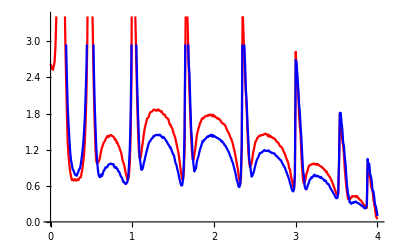

```mathematica
Show[ListLinePlot[%36,PlotStyle->Red],ListLinePlot[%37,PlotStyle->Blue]]
```

```mathematica
Export["/home/shardulmukim/PhD/fwi/8imp5.dat",%31]
```

/home/shardulmukim/PhD/fwi/8imp5.dat

```mathematica
SystemOpen["/home/shardulmukim/PhD/fwi/8imp5.dat"]
```

```mathematica
Export["/home/shardulmukim/PhD/fwi/8imp4.dat",%32]
```

/home/shardulmukim/PhD/fwi/8imp4.dat

```mathematica
Export["/home/shardulmukim/PhD/fwi/8imp3.dat",%33]
```

/home/shardulmukim/PhD/fwi/8imp3.dat

```mathematica
Export["/home/shardulmukim/PhD/fwi/8imp6.dat",%34]
```

/home/shardulmukim/PhD/fwi/8imp6.dat

```mathematica
Export["/home/shardulmukim/PhD/fwi/8imp7.dat",%35]
```

/home/shardulmukim/PhD/fwi/8imp7.dat

```mathematica
Export["/home/shardulmukim/PhD/fwi/8imp8.dat",%36]
```

/home/shardulmukim/PhD/fwi/8imp8.dat

```mathematica
Export["/home/shardulmukim/PhD/fwi/8imp9.dat",%37]
```

/home/shardulmukim/PhD/fwi/8imp9.dat

```mathematica
Tally[{imp7,imp10,imp9,imp,imp1,imp,imp,imp,imp9,imp9,imp5,imp,imp8,imp11,imp13,imp,imp3,imp3,imp,imp,imp14,imp,imp13,imp8,imp,imp11,imp,imp8,imp7,imp,imp,imp,imp5,imp,imp,imp14,imp,imp5,imp10,imp,imp10,imp2,imp6,imp,imp2,imp11,imp,imp6,imp4,imp,imp,imp,imp,imp6,imp,imp,imp,imp4,imp1,imp,imp10,imp,imp2,imp13,imp,imp4,imp14,imp7,imp,imp11,imp8,imp4,imp7,imp,imp12,imp,imp,imp12,imp14,imp,imp,imp3,imp5,imp,imp1,imp,imp,imp12,imp13,imp2,imp1,imp,imp6,imp12,imp,imp3,imp9,imp,imp,imp}]
```

{{imp7,4},{imp10,4},{imp9,4},{imp,44},{imp1,4},{imp5,4},{imp8,4},{imp11,4},{imp13,4},{imp3,4},{imp14,4},{imp2,4},{imp6,4},{imp4,4},{imp12,4}}

```mathematica
Clear[imp,imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp13,imp14]
```

```mathematica
56/800
```

7/100

```mathematica
N[7/100]
```

0.07